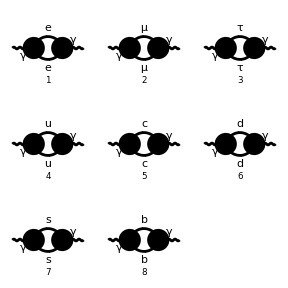

FeynArtsGraphics()(([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | Null))

```mathematica
diaggalightfermion=InsertFields[topoself,process2,InsertionLevel->{Particles},ExcludeParticles->{F[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[3,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diaggalightfermion,SheetHeader->None,Numbering->Simple]
```

```mathematica
ampggafselflightfermion=FCFAConvert[CreateFeynAmp[diaggalightfermion, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]],SMP["m_b"]->0,SMP["m_e"]->0,SMP["m_mu"]->0,SMP["m_tau"]->0,SMP["m_u"]->0,SMP["m_d"]->0,SMP["m_s"]->0,SMP["m_c"]->0}]
```

-(3 SumOver(Col3,3) tr((-(γ·q)).(2/3 ⅈ √π √α γ^ν).(γ·(k-q)).(2/3 ⅈ √π √α γ^μ)))/(q^2.(q-k)^2)-(2 SumOver(Col3,3) tr((-(γ·q)).(-4/3 ⅈ √π √α γ^ν).(γ·(k-q)).(-4/3 ⅈ √π √α γ^μ)))/(q^2.(q-k)^2)-(3 tr((-(γ·q)).(2 ⅈ √π √α γ^ν).(γ·(k-q)).(2 ⅈ √π √α γ^μ)))/(q^2.(q-k)^2)

```mathematica
transversegalightfermion=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]])ampggafselflightfermion/.SumOver[SUNFIndex[Col3],3]-> 3//Contract//DiracSimplify
```

(9 tr(-8/9 π α (k·q) (γ·q).(γ·k)-4/9 π α k^2 (γ·q).(γ·k)+4/9 π α k^2 q^2+8/9 π α k^2 (k·q)))/((D-1) k^2 q^2.(q-k)^2)+(6 tr(-32/9 π α (k·q) (γ·q).(γ·k)-16/9 π α k^2 (γ·q).(γ·k)+16/9 π α k^2 q^2+32/9 π α k^2 (k·q)))/((D-1) k^2 q^2.(q-k)^2)+(3 tr(-8 π α (k·q) (γ·q).(γ·k)-4 π α k^2 (γ·q).(γ·k)+4 π α k^2 q^2+8 π α k^2 (k·q)))/((D-1) k^2 q^2.(q-k)^2)-(9 tr(-4/9 π α D (γ·q).(γ·k)+4/9 π α D q^2+8/9 π α (γ·q).(γ·k)-8/9 π α q^2))/((D-1) q^2.(q-k)^2)-(6 tr(-16/9 π α D (γ·q).(γ·k)+16/9 π α D q^2+32/9 π α (γ·q).(γ·k)-32/9 π α q^2))/((D-1) q^2.(q-k)^2)-(3 tr(-4 π α D (γ·q).(γ·k)+4 π α D q^2+8 π α (γ·q).(γ·k)-8 π α q^2))/((D-1) q^2.(q-k)^2)

```mathematica
Σγγlightfermion=-ⅈ/(16 π^2)TID[transversegalightfermion/.DiracTrace-> Tr,q,ToPaVe-> True]//DiracSimplify//Expand
```

(20 π α k^2 B_0(k^2,0,0))/(3 (1-D))-(10 π α D k^2 B_0(k^2,0,0))/(3 (1-D))

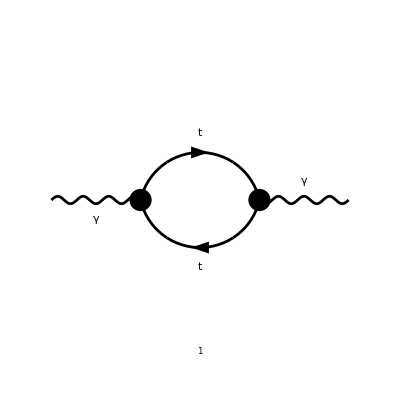

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

-(SumOver(Col3,3) tr((m_t-γ·q).(-4/3 ⅈ √π √α γ^ν).(γ·(k-q)+m_t).(-4/3 ⅈ √π √α γ^μ)))/((q^2-m_t^2).((q-k)^2-m_t^2))

(3 tr(32/9 π α m_t γ·k (k·q)-16/9 π α k^2 m_t γ·k-16/9 π α k^2 m_t^2-32/9 π α (k·q) (γ·q).(γ·k)+16/9 π α k^2 (γ·q).(γ·k)+16/9 π α k^2 q^2))/((D-1) k^2 (q^2-m_t^2).((q-k)^2-m_t^2))-(3 tr(-16/9 π α D m_t γ·k-16/9 π α D (γ·q).(γ·k)-16/9 π α D m_t^2+16/9 π α D q^2+32/9 π α (γ·q).(γ·k)+32/9 π α m_t γ·q-32/9 π α q^2))/((D-1) (q^2-m_t^2).((q-k)^2-m_t^2))

```mathematica
topquark=InsertFields[topoself,process2,InsertionLevel->{Particles},ExcludeParticles->{F[1],V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[2],F[3,{1}],F[3,{2}],F[4,{1}],F[4,{2}],F[4,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[topquark,SheetHeader->None,Numbering->Simple]
ampggafselftopquark=FCFAConvert[CreateFeynAmp[topquark, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
transversegatopquark=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]])ampggafselftopquark/.SumOver[SUNFIndex[Col3],3]-> 3//Contract//DiracSimplify
```

```mathematica
Σγγtop=-ⅈ/(16 π^2)TID[transversegatopquark/.DiracTrace-> Tr,q,ToPaVe-> True]//DiracSimplify//Expand
```

-(8 π α m_t^2 B_0(k^2,m_t^2,m_t^2))/(3 (1-D))-(2 π α D k^2 B_0(k^2,m_t^2,m_t^2))/(3 (1-D))+(4 π α k^2 B_0(k^2,m_t^2,m_t^2))/(3 (1-D))+(4 π α D A_0(m_t^2))/(3 (1-D))-(8 π α A_0(m_t^2))/(3 (1-D))

```mathematica
Πγγlighfermion[k_]= 1/Pair[Momentum[k,D],Momentum[k,D]] Σγγlightfermion/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2//Expand
```

(20 π α B_0(k^2,0,0))/(3 (1-D))-(10 π α D B_0(k^2,0,0))/(3 (1-D))

```mathematica
Πγγtop[k_]=D[Σγγtop,Pair[Momentum[k,D],Momentum[k,D]]]/.{Pair[Momentum[k,D],Momentum[k,D]]-> k^2}//Expand
```

-(2 π α D B_0(k^2,m_t^2,m_t^2))/(3 (1-D))+(4 π α B_0(k^2,m_t^2,m_t^2))/(3 (1-D))-(2 π α D k^2 DB0(k^2,m_t^2,m_t^2))/(3 (1-D))+(4 π α k^2 DB0(k^2,m_t^2,m_t^2))/(3 (1-D))-(8 π α m_t^2 DB0(k^2,m_t^2,m_t^2))/(3 (1-D))

```mathematica
Πγγtop[0]=Normal[Series[Πγγtop[k],{k,0,0}]]/.B0[0,y_,y_]-> (D/2-1)A0[y]/y//Expand
```

(8 π α m_t^2 DB0(0,m_t^2,m_t^2))/(3 (D-1))+(π α D^2 A_0(m_t^2))/(3 (D-1) m_t^2)-(4 π α D A_0(m_t^2))/(3 (D-1) m_t^2)+(4 π α A_0(m_t^2))/(3 (D-1) m_t^2)

```mathematica
Πγγ[k_]= π^2 Δα+Πγγlighfermion[SMP["m_Z"]]+Πγγtop[0]/.{B0[0,y_,y_]-> (D/2-1)A0[y]/y,DB0[0,s_,s_]-> -1/6(D/2-1)(D/2-2) A0[s]/s^2}//Expand
```

-(10 π α D B_0(m_Z^2,0,0))/(3 (1-D))+(20 π α B_0(m_Z^2,0,0))/(3 (1-D))+(2 π α D^2 A_0(m_t^2))/(9 (D-1) m_t^2)-(2 π α D A_0(m_t^2))/(3 (D-1) m_t^2)+(4 π α A_0(m_t^2))/(9 (D-1) m_t^2)+π^2 Δα

```mathematica
Πγγ[0]
```

-(10 π α D B_0(m_Z^2,0,0))/(3 (1-D))+(20 π α B_0(m_Z^2,0,0))/(3 (1-D))+(2 π α D^2 A_0(m_t^2))/(9 (D-1) m_t^2)-(2 π α D A_0(m_t^2))/(3 (D-1) m_t^2)+(4 π α A_0(m_t^2))/(9 (D-1) m_t^2)+π^2 Δα

```mathematica
Collect[Πγγ[0],{B0[SMP["m_Z"]^2,0,0],A0[SMP["m_t"]^2]}]
```

((20 π α)/(3 (1-D))-(10 π α D)/(3 (1-D))) B_0(m_Z^2,0,0)+A_0(m_t^2) ((2 π α D^2)/(9 (D-1) m_t^2)-(2 π α D)/(3 (D-1) m_t^2)+(4 π α)/(9 (D-1) m_t^2))+π^2 Δα

```mathematica
(*Ayres's counterterm of coupling*)
Collect[2 π^2 δZe//Expand,{B0[SMP["m_Z"]^2,0,0],A0[SMP["m_t"]^2]}]
```

((10 π α D)/(3 (D-1))-(20 π α)/(3 (D-1))) B_0(m_Z^2,0,0)+A_0(m_t^2) ((2 π α D)/(9 m_t^2)-(4 π α)/(9 m_t^2))+π^2 Δα

```mathematica
(*derivative of my Σγγtop*)
```

```mathematica
Collect[Πγγtop[0]/.{B0[0,y_,y_]-> A0[y]/y,DB0[0,s_,s_]-> -1/6(D/2-1)(D/2-2) A0[s]/s^2}//Expand,A0[SMP["m_t"]^2]]//FullSimplify
```

(2 π α (D-2) A_0(m_t^2))/(9 m_t^2)

```mathematica
(*Ayres's top-loop gamma gamma self*)
-(EL^2*(-2+$D)*A0[MT^2])/(3*Pi^2*(-1+$D))+(EL^2*(4*MT^2+p2*(-2+$D))*B0[p2,MT^2,MT^2])/(6*Pi^2*(-1+$D))/.{$D-> D,EL^2-> 4π SMP["alpha_fs"],MT^2->SMP["m_t"]^2,B0Re[MZ^2,0,0]-> B0[SMP["m_Z"]^2,0,0],deltaAlpha->Δα,1/MT^2-> 1/SMP["m_t"]^2,p2-> Pair[Momentum[k,D],Momentum[k,D]]}//Expand
```

(8 α m_t^2 B_0(k^2,m_t^2,m_t^2))/(3 π (D-1))+(2 α D k^2 B_0(k^2,m_t^2,m_t^2))/(3 π (D-1))-(4 α k^2 B_0(k^2,m_t^2,m_t^2))/(3 π (D-1))-(4 α D A_0(m_t^2))/(3 π (D-1))+(8 α A_0(m_t^2))/(3 π (D-1))

```mathematica
(*my top-loop gamma gamma self*)
```

```mathematica
Σγγtop//Expand
```

(8 π α m_t^2 B_0(k^2,m_t^2,m_t^2))/(3 (D-1))+(2 π α D k^2 B_0(k^2,m_t^2,m_t^2))/(3 (D-1))-(4 π α k^2 B_0(k^2,m_t^2,m_t^2))/(3 (D-1))-(4 π α D A_0(m_t^2))/(3 (D-1))+(8 π α A_0(m_t^2))/(3 (D-1))

```mathematica
Πγγtop[0]/.DB0[0,s_,s_]-> -1/6(D/2-1)(D/2-2) A0[s]/s^2//Expand
```

(2 π α D^2 A_0(m_t^2))/(9 (D-1) m_t^2)-(2 π α D A_0(m_t^2))/(3 (D-1) m_t^2)+(4 π α A_0(m_t^2))/(9 (D-1) m_t^2)